```mathematica
start2=Monitor[Table[With[{first=deps2[[k,1]]},{Chrom5[first],VertexCount[ReadGrof[ first]],first}],{k,1,Length[deps2]}],N[k/Length[deps2]*100]]
```

{{120,4,1},{240,5,2},{240,5,2},{480,6,3},{480,6,3},{480,6,3},{480,6,3},{780,6,4},{960,7,5},{960,7,5},{960,7,5},{960,7,5},{960,7,5},{960,7,5},{1560,7,6},{1560,7,6},{1560,7,6},{1800,7,7},{1800,7,7},{960,7,8},{960,7,8},{960,7,8},{960,7,8},1365007,{61440,13,58713},{61440,13,58713},{61440,13,58713},{61440,13,58713},{61440,13,58713},{99840,13,58714},{99840,13,58714},{99840,13,58714},{99840,13,58714},{99840,13,58714},{99840,13,58714},{99840,13,58714},{99840,13,58714},{926640,13,58715},{926640,13,58715},{61440,13,58716},{61440,13,58716},{61440,13,58716},{61440,13,58716},{61440,13,58716},{61440,13,58716},{61440,13,58716},{61440,13,58716}}
 |  |  |  |

```mathematica
deps2[[1,1]]
```

1

```mathematica
Table[{k,Max[Map[#[[1]]&,Select[start2,#[[2]]==k&]]]/60},{k,4,13}]
```

{{4,2},{5,4},{6,13},{7,30},{8,83},{9,224},{10,633},{11,1810},{12,5263},{13,15444}}

```mathematica
Get["d:\\start2.m"]
```

{{120,4,1},{240,5,2},{240,5,2},{480,6,3},{480,6,3},{480,6,3},{480,6,3},{780,6,4},{960,7,5},{960,7,5},{960,7,5},{960,7,5},{960,7,5},{960,7,5},{1560,7,6},{1560,7,6},{1560,7,6},{1800,7,7},{1800,7,7},{960,7,8},{960,7,8},{960,7,8},{960,7,8},1365007,{61440,13,58713},{61440,13,58713},{61440,13,58713},{61440,13,58713},{61440,13,58713},{99840,13,58714},{99840,13,58714},{99840,13,58714},{99840,13,58714},{99840,13,58714},{99840,13,58714},{99840,13,58714},{99840,13,58714},{926640,13,58715},{926640,13,58715},{61440,13,58716},{61440,13,58716},{61440,13,58716},{61440,13,58716},{61440,13,58716},{61440,13,58716},{61440,13,58716},{61440,13,58716}}
 |  |  |  |

```mathematica
Save["d:\\start2.m",{start2}]
```

```mathematica
Map[#[[2]]&,{{4,1},{5,2},{6,13/2},{7,15},{8,83/2},{9,112},{10,633/2},{11,905},{12,5263/2},{13,7722}}]*2
```

{2,4,13,30,83,224,633,1810,5263,15444}

```mathematica
FindGeneratingFunction[{2,4,13,30,83,224,633,1810,5263,15444},x]
```

(2-4 x-x^2-6 x^3)/(1-4 x+x^2+6 x^3)

```mathematica
FindSequenceFunction[{2,4,13,30,83,224,633,1810,5263,15444},x]
```

DifferenceRoot[{y,n}↦{6 y(n)+y(n+1)-4 y(n+2)+y(n+3)==0,y(1)==2,y(2)==4,y(3)==13,y(4)==30}][x]

```mathematica
Table[MaxFive[k],{k,1,10}]
```

{2,4,13,36,107,314,933,2776,8287,24774}

```mathematica
FindSequenceFunction[{2,4,13,30,83,224,633,1810,5263,15444}]
```

DifferenceRoot[Function[{y,n},{6 y[n]+y[1+n]-4 y[2+n]+y[3+n]==0,y[1]==2,y[2]==4,y[3]==13,y[4]==30}]]

```mathematica
LinearRecurrence[{4,-1,-6},{2,4,13},10]
```

{2,4,13,36,107,314,933,2776,8287,24774}

```mathematica
RSolve[a[n+3]==-6 a[n]-a[n+1]+4 a[n+2],a[n],n]
```

{{a[n]→(-1)^n C[1]+2^n C[2]+3^n C[3]}}

```mathematica
Prob[n_]:=(-1)^n x+2^n y+3^n z+q*4^n
```

```mathematica
Solve[{Prob[1]==2,Prob[2]==3,Prob[3]==13,Prob[4]==30},{x,y,z,q}]
```

{{x→-19/20,y→-3/4,z→13/12,q→-7/40}}

```mathematica
Prob2[n_]:=(-1)^n *(-19/20)+2^n *(-3/4)+3^n (13/12)+4^n*(-7/40)
```

```mathematica
Table[Prob2[k],{k,1,10}]
```

{2,3,13,30,61,24,-593,-4554,-24935,-120300}

```mathematica
start2=Monitor[Table[With[{first=deps2[[k,1]]},{Chrom5[first],VertexCount[ReadGrof[ first]],first}],{k,1,Length[deps2]}],N[k/Length[deps2]*100]]
```

```mathematica
Select[start2,#[[1]]==15444*60&]
```

{{926640,13,58715},{926640,13,58715}}

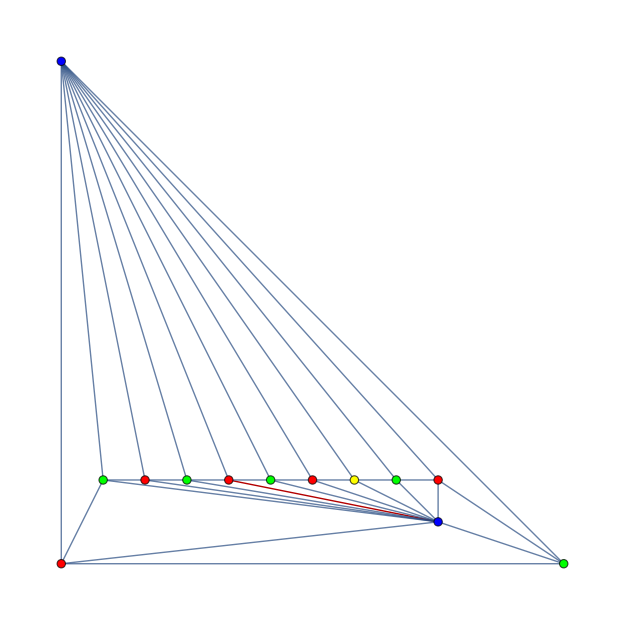

```mathematica
PaintGraph2First[ReadGrof[58715],"x1==1&&x2==2&&x3==3",GraphHighlight->{3<->4}]
```

```mathematica
IsomorphicGraphQ[ReadGrof[58715],JacobsThalGraph[9]]
```

True

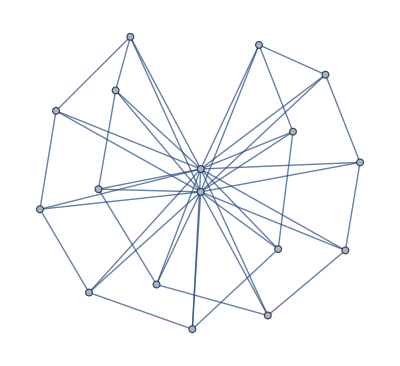

```mathematica
JacobsThalGraph[13]
```

```mathematica
Table[ChromaticPolynomial[JacobsThalGraph[k],5]/60,{k,1,10}]
```

{4,13,30,83,224,633,1810,5263,15444,45653}

```mathematica
2,4,13,30,83,224,633,1810,5263,15444
```

```mathematica
TableForm[FactorInteger[Table[ChromaticPolynomial[JacobsThalGraph[k],6]/120,{k,1,10}]],TableDepth->1]
```

{{3,2}}
{{2,1},{17,1}}
{{3,1},{37,1}}
{{2,2},{97,1}}
{{3,1},{5,1},{7,1},{13,1}}
{{2,1},{2459,1}}
{{3,2},{2003,1}}
{{2,3},{37,1},{227,1}}
{{3,1},{11,1},{43,1},{179,1}}
{{2,1},{389,1},{1249,1}}

```mathematica
2^3*3*5
```

120

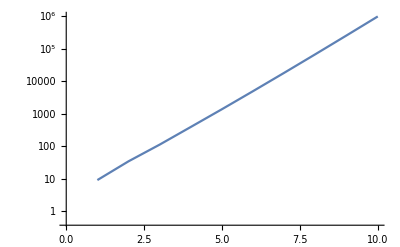

```mathematica
ListLogPlot[Table[ChromaticPolynomial[JacobsThalGraph[k],6]/120,{k,1,10}],Joined->True]
```

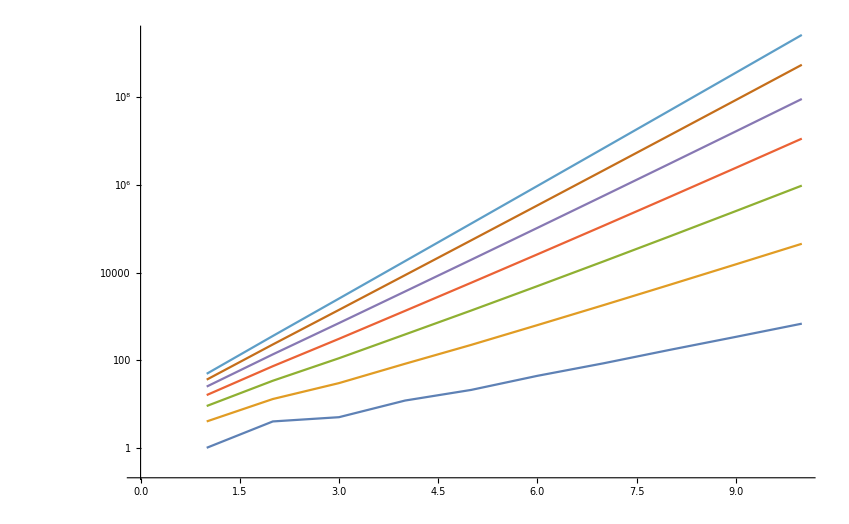

```mathematica
ListLogPlot[Table[Table[ChromaticPolynomial[JacobsThalGraph[k],w]/Factors235[[w-3]],{k,1,10}],{w,4,10}],Joined->True]
```

```mathematica
Table[Fold[GCD,Table[ChromaticPolynomial[JacobsThalGraph[k],w],{k,1,12}]],{w,4,20}]
```

```mathematica
Factors235:={24,60,120,210,336,504,720,990,1320,1716,2184,2730,3360,4080,4896,5814,6840}
```

```mathematica
Fold[GCD,Table[ChromaticPolynomial[JacobsThalGraph[k],8],{k,1,10}]]
```

336

```mathematica
GCD[8400,45696,236880,1248576,6614160,35312256,189996240,1030604736,5636751120,31086134016]
```

336

```mathematica
2^4*3*7
```

336

```mathematica
2*3*5*7
```

210

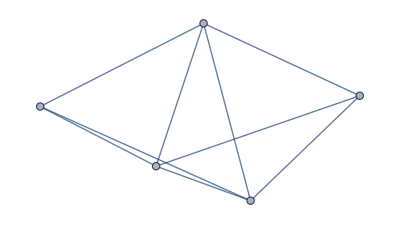

```mathematica
JacobsThalGraph[1]
```

```mathematica
GraphAutomorphismGroup[JacobsThalGraph[20]]
```

PermutationGroup[{Cycles[{{3,4}}],Cycles[{{2,5},{6,7},{8,24},{9,23},{10,22},{11,21},{12,20},{13,19},{14,18},{15,17}}],Cycles[{{1,2,6,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,5}}]}]

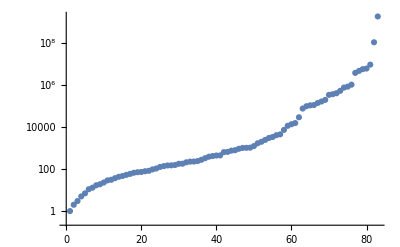

```mathematica
ListLogPlot[DeleteDuplicates[Map[First,Sort[Flatten[FactorInteger[Table[Table[ChromaticPolynomial[JacobsThalGraph[k],w]/Factors235[[w-3]],{k,1,10}],{w,4,13}]],2]]]]]
```

```mathematica
Det[Table[Table[ChromaticPolynomial[JacobsThalGraph[k],w]/Factors235[[w-3]],{k,1,10}],{w,4,13}]]
```

-140130991673839112201661579264000000

```mathematica
FactorInteger[140130991673839112201661579264000000]
```

{{2,37},{3,21},{5,6},{7,3},{13,1},{1399009,1}}

```mathematica
MatrixForm[Table[Table[ChromaticPolynomial[JacobsThalGraph[k],w]/Factors235[[w-3]],{k,1,15}],{w,4,15+3}]]
```

(1 | 4 | 5 | 12 | 21 | 44 | 85 | 172 | 341 | 684 | 1365 | 2732 | 5461 | 10924 | 21845
4 | 13 | 30 | 83 | 224 | 633 | 1810 | 5263 | 15444 | 45653 | 135590 | 404043 | 1206664 | 3609073 | 10805370
9 | 34 | 111 | 388 | 1365 | 4918 | 18027 | 67192 | 254001 | 971722 | 3754023 | 14617516 | 57274317 | 225510046 | 891278499
16 | 73 | 308 | 1341 | 5880 | 26129 | 117532 | 535237 | 2466464 | 11493465 | 54111876 | 257137613 | 1232000968 | 5945256481 | 28867288940
25 | 136 | 705 | 3716 | 19685 | 105096 | 565465 | 3067276 | 16776045 | 92518256 | 514419425 | 2883066036 | 16281143605 | 92600598616 | 530172276585
36 | 229 | 1410 | 8767 | 54696 | 342889 | 2160270 | 13682227 | 87137556 | 558134749 | 3595974330 | 23306006887 | 151947167616 | 996460889809 | 6572210527590
49 | 358 | 2555 | 18348 | 132069 | 953618 | 6908335 | 50222488 | 366470489 | 2684598078 | 19746623715 | 145861863428 | 1082117023309 | 8063490997738 | 60353811660695
64 | 529 | 4296 | 35033 | 286160 | 2342433 | 19217752 | 158046697 | 1303115616 | 10773603377 | 89326932968 | 742858417401 | 6197053922032 | 51864110621761 | 435501998183544
81 | 748 | 6813 | 62236 | 569205 | 5213764 | 47832957 | 439587532 | 4047196869 | 37333862740 | 345095673741 | 3196770154588 | 29680022300373 | 276211109794276 | 2576809079057565
100 | 1021 | 10310 | 104331 | 1056720 | 10714841 | 108772330 | 1105586551 | 11252361140 | 114685063461 | 1170626607150 | 11967801769571 | 122554910374360 | 1257194923208881 | 12920053246206770
121 | 1354 | 15015 | 166772 | 1853621 | 20619534 | 229571155 | 2558358232 | 28538846721 | 318690188114 | 3562746559295 | 39876066032892 | 446866972929421 | 5014299661035094 | 56342451777123435
144 | 1753 | 21180 | 256213 | 3101064 | 37557553 | 455172660 | 5520338413 | 67001525184 | 813865337353 | 9894395504940 | 120396894996613 | 1466396676144504 | 17878001284141153 | 218192150624986020
169 | 2224 | 29081 | 380628 | 4984005 | 65294048 | 855850177 | 11224438252 | 147295100381 | 1934119948632 | 25413530343513 | 334155488624036 | 4396935670329397 | 57900964169319376 | 763083740571672689
196 | 2773 | 39018 | 549431 | 7739480 | 109064649 | 1537583782 | 21686353627 | 306011660724 | 4320203899565 | 61023464335106 | 862437646809663 | 12195764247107728 | 172565257336095121 | 2443281970854135390
225 | 3406 | 51315 | 773596 | 11665605 | 175970986 | 2655355095 | 40082971576 | 605286895785 | 9143980591366 | 138194543343675 | 2089475501726356 | 31607050151034765 | 478344434267752546 | 7242985426051985055)

```mathematica
FindGeneratingFunction[{{{9,, 34,, 111,, 388, ,1365, ,4918, ,18027,, 67192,, 254001,, 971722}}},z]
```

```mathematica
Table[FindGeneratingFunction[Table[ChromaticPolynomial[JacobsThalGraph[k],w]/Factors235[[w-3]],{k,1,15}],x],{w,4,15+3}]
```

{(1+2 x-4 x^2)/(1-2 x-x^2+2 x^3),(4-3 x-18 x^2)/(1-4 x+x^2+6 x^3),(9-20 x-48 x^2)/(1-6 x+5 x^2+12 x^3),(16-55 x-100 x^2)/(1-8 x+11 x^2+20 x^3),(25-114 x-180 x^2)/(1-10 x+19 x^2+30 x^3),(36-203 x-294 x^2)/(1-12 x+29 x^2+42 x^3),(49-328 x-448 x^2)/(1-14 x+41 x^2+56 x^3),(64-495 x-648 x^2)/(1-16 x+55 x^2+72 x^3),(81-710 x-900 x^2)/(1-18 x+71 x^2+90 x^3),(100-979 x-1210 x^2)/(1-20 x+89 x^2+110 x^3),(121-1308 x-1584 x^2)/(1-22 x+109 x^2+132 x^3),(144-1703 x-2028 x^2)/(1-24 x+131 x^2+156 x^3),(169-2170 x-2548 x^2)/(1-26 x+155 x^2+182 x^3),(196-2715 x-3150 x^2)/(1-28 x+181 x^2+210 x^3),(225-3344 x-3840 x^2)/(1-30 x+209 x^2+240 x^3)}

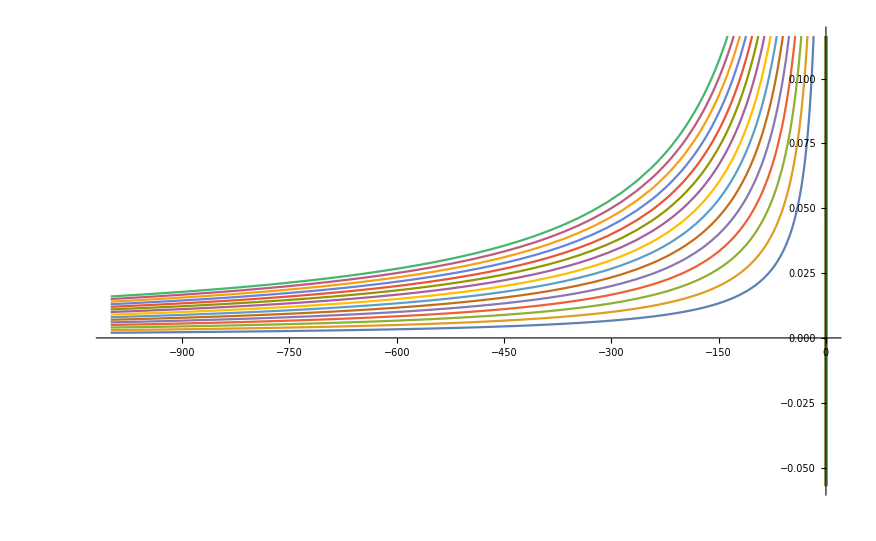

```mathematica
Plot[{(1+2 x-4 x^2)/(1-2 x-x^2+2 x^3),(4-3 x-18 x^2)/(1-4 x+x^2+6 x^3),(9-20 x-48 x^2)/(1-6 x+5 x^2+12 x^3),(16-55 x-100 x^2)/(1-8 x+11 x^2+20 x^3),(25-114 x-180 x^2)/(1-10 x+19 x^2+30 x^3),(36-203 x-294 x^2)/(1-12 x+29 x^2+42 x^3),(49-328 x-448 x^2)/(1-14 x+41 x^2+56 x^3),(64-495 x-648 x^2)/(1-16 x+55 x^2+72 x^3),(81-710 x-900 x^2)/(1-18 x+71 x^2+90 x^3),(100-979 x-1210 x^2)/(1-20 x+89 x^2+110 x^3),(121-1308 x-1584 x^2)/(1-22 x+109 x^2+132 x^3),(144-1703 x-2028 x^2)/(1-24 x+131 x^2+156 x^3),(169-2170 x-2548 x^2)/(1-26 x+155 x^2+182 x^3),(196-2715 x-3150 x^2)/(1-28 x+181 x^2+210 x^3),(225-3344 x-3840 x^2)/(1-30 x+209 x^2+240 x^3)},{x,-1000,1}]
```

```mathematica
Table[FindGeneratingFunction[Table[ChromaticPolynomial[JacobsThalGraph[k],w],{k,1,15}],x],{w,4,15+3}]
```

{-(24 (-1-2 x+4 x^2))/(1-2 x-x^2+2 x^3),-(60 (-4+3 x+18 x^2))/(1-4 x+x^2+6 x^3),-(120 (-9+20 x+48 x^2))/(1-6 x+5 x^2+12 x^3),-(210 (-16+55 x+100 x^2))/(1-8 x+11 x^2+20 x^3),-(336 (-25+114 x+180 x^2))/(1-10 x+19 x^2+30 x^3),-(504 (-36+203 x+294 x^2))/(1-12 x+29 x^2+42 x^3),-(720 (-49+328 x+448 x^2))/(1-14 x+41 x^2+56 x^3),-(990 (-64+495 x+648 x^2))/(1-16 x+55 x^2+72 x^3),-(1320 (-81+710 x+900 x^2))/(1-18 x+71 x^2+90 x^3),-(1716 (-100+979 x+1210 x^2))/(1-20 x+89 x^2+110 x^3),-(2184 (-121+1308 x+1584 x^2))/(1-22 x+109 x^2+132 x^3),-(2730 (-144+1703 x+2028 x^2))/(1-24 x+131 x^2+156 x^3),-(3360 (-169+2170 x+2548 x^2))/(1-26 x+155 x^2+182 x^3),-(4080 (-196+2715 x+3150 x^2))/(1-28 x+181 x^2+210 x^3),-(4896 (-225+3344 x+3840 x^2))/(1-30 x+209 x^2+240 x^3)}

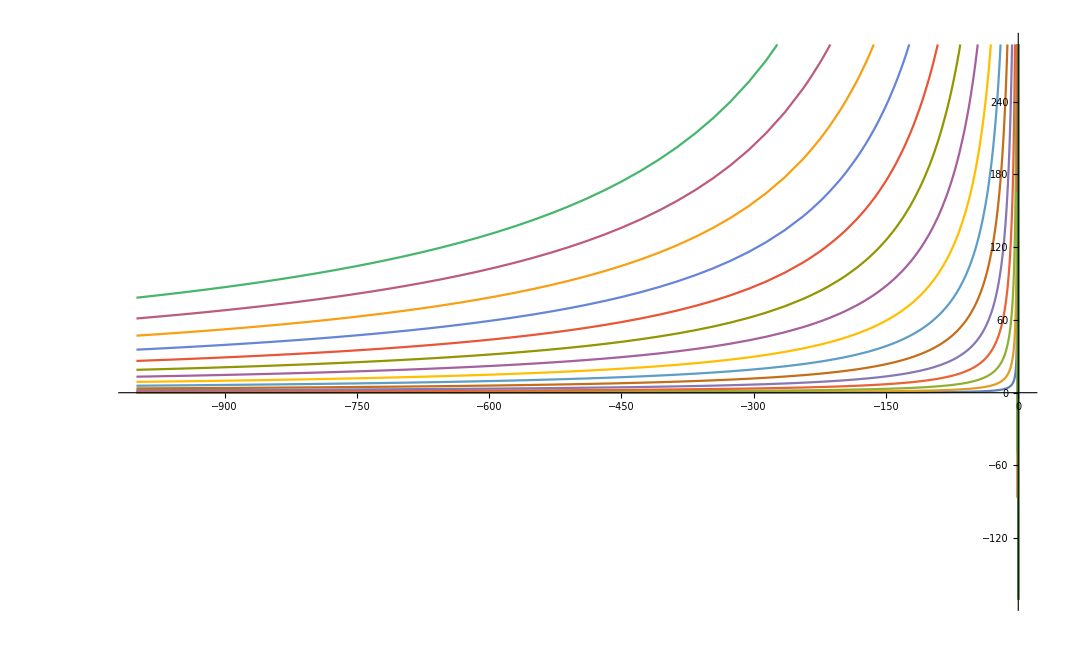

```mathematica
Plot[{-(24 (-1-2 x+4 x^2))/(1-2 x-x^2+2 x^3),-(60 (-4+3 x+18 x^2))/(1-4 x+x^2+6 x^3),-(120 (-9+20 x+48 x^2))/(1-6 x+5 x^2+12 x^3),-(210 (-16+55 x+100 x^2))/(1-8 x+11 x^2+20 x^3),-(336 (-25+114 x+180 x^2))/(1-10 x+19 x^2+30 x^3),-(504 (-36+203 x+294 x^2))/(1-12 x+29 x^2+42 x^3),-(720 (-49+328 x+448 x^2))/(1-14 x+41 x^2+56 x^3),-(990 (-64+495 x+648 x^2))/(1-16 x+55 x^2+72 x^3),-(1320 (-81+710 x+900 x^2))/(1-18 x+71 x^2+90 x^3),-(1716 (-100+979 x+1210 x^2))/(1-20 x+89 x^2+110 x^3),-(2184 (-121+1308 x+1584 x^2))/(1-22 x+109 x^2+132 x^3),-(2730 (-144+1703 x+2028 x^2))/(1-24 x+131 x^2+156 x^3),-(3360 (-169+2170 x+2548 x^2))/(1-26 x+155 x^2+182 x^3),-(4080 (-196+2715 x+3150 x^2))/(1-28 x+181 x^2+210 x^3),-(4896 (-225+3344 x+3840 x^2))/(1-30 x+209 x^2+240 x^3)},{x,-1000,1}]
```

```mathematica
RSolve[6 y(n)+y(n+1)-4 y(n+2)+y(n+3)==0,y(1)==2,y(2)==4,y(3)==13,y(4)==30]
```

RSolve::dsvar: 2\ y == 4 cannot be used as a variable.

RSolve[6 n y+(1+n) y-4 (2+n) y+(3+n) y==0,y==2,2 y==4,3 y==13,4 y==30]

```mathematica
DSolve[-6a[n]==a[n+1]-4a[n+2]+a[n+3]&&a[1]==2&&a[2]==2&&a[3]==13&&a[4]==30,a[n],n]
```

DSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in {-6\ a[n] == a[1 + n] - 4\ a[2 + n] + a[3 + n]} should literally match the independent variables.

DSolve[-6 a[n]==a[1+n]-4 a[2+n]+a[3+n]&&a[1]==2&&a[2]==2&&a[3]==13&&a[4]==30,a[n],n]

```mathematica
ListPointPlot3D[Flatten[Table[Table[{w,k,N[Log[ChromaticPolynomial[JacobsThalGraph[k],w]]]},{k,1,15}],{w,4,15+3}],1]]
```

-Graphics3D-

```mathematica
Flatten[Table[Table[Map[{w,k,#[[1]]}&,FactorInteger[ChromaticPolynomial[JacobsThalGraph[k],w]]],{k,1,5}],{w,4,5+3}],2]
```

{{4,1,2},{4,1,3},{4,2,2},{4,2,3},{4,3,2},{4,3,3},{4,3,5},{4,4,2},{4,4,3},{4,5,2},{4,5,3},{4,5,7},{5,1,2},{5,1,3},{5,1,5},{5,2,2},{5,2,3},{5,2,5},{5,2,13},{5,3,2},{5,3,3},{5,3,5},{5,4,2},{5,4,3},{5,4,5},{5,4,83},{5,5,2},{5,5,3},{5,5,5},{5,5,7},{6,1,2},{6,1,3},{6,1,5},{6,2,2},{6,2,3},{6,2,5},{6,2,17},{6,3,2},{6,3,3},{6,3,5},{6,3,37},{6,4,2},{6,4,3},{6,4,5},{6,4,97},{6,5,2},{6,5,3},{6,5,5},{6,5,7},{6,5,13},{7,1,2},{7,1,3},{7,1,5},{7,1,7},{7,2,2},{7,2,3},{7,2,5},{7,2,7},{7,2,73},{7,3,2},{7,3,3},{7,3,5},{7,3,7},{7,3,11},{7,4,2},{7,4,3},{7,4,5},{7,4,7},{7,4,149},{7,5,2},{7,5,3},{7,5,5},{7,5,7},{8,1,2},{8,1,3},{8,1,5},{8,1,7},{8,2,2},{8,2,3},{8,2,7},{8,2,17},{8,3,2},{8,3,3},{8,3,5},{8,3,7},{8,3,47},{8,4,2},{8,4,3},{8,4,7},{8,4,929},{8,5,2},{8,5,3},{8,5,5},{8,5,7},{8,5,31},{8,5,127}}

```mathematica
ListPlot3D[Table[Table[Map[{n,#[[1]]}&,FactorInteger[ChromaticPolynomial[JacobsThalGraph[k],w]]],{k,1,20}],{w,4,20+3}]]
```

-Graphics3D-

```mathematica
FactorInteger[ChromaticPolynomial[JacobsThalGraph[10],10]]
```

{{2,5},{3,3},{5,1},{17,1},{31,1},{849019,1}}

```mathematica
Flatten[Table[Table[{w,k,ChromaticPolynomial[JacobsThalGraph[k],w]/(w!/(w-3)!)},{k,1,10}],{w,4,10+3}],1]
```

{{4,1,1},{4,2,4},{4,3,5},{4,4,12},{4,5,21},{4,6,44},{4,7,85},{4,8,172},{4,9,341},{4,10,684},{5,1,4},{5,2,13},{5,3,30},{5,4,83},{5,5,224},{5,6,633},{5,7,1810},{5,8,5263},{5,9,15444},{5,10,45653},{6,1,9},{6,2,34},{6,3,111},{6,4,388},{6,5,1365},{6,6,4918},{6,7,18027},{6,8,67192},{6,9,254001},{6,10,971722},{7,1,16},{7,2,73},{7,3,308},{7,4,1341},{7,5,5880},{7,6,26129},{7,7,117532},{7,8,535237},{7,9,2466464},{7,10,11493465},{8,1,25},{8,2,136},{8,3,705},{8,4,3716},{8,5,19685},{8,6,105096},{8,7,565465},{8,8,3067276},{8,9,16776045},{8,10,92518256},{9,1,36},{9,2,229},{9,3,1410},{9,4,8767},{9,5,54696},{9,6,342889},{9,7,2160270},{9,8,13682227},{9,9,87137556},{9,10,558134749},{10,1,49},{10,2,358},{10,3,2555},{10,4,18348},{10,5,132069},{10,6,953618},{10,7,6908335},{10,8,50222488},{10,9,366470489},{10,10,2684598078},{11,1,64},{11,2,529},{11,3,4296},{11,4,35033},{11,5,286160},{11,6,2342433},{11,7,19217752},{11,8,158046697},{11,9,1303115616},{11,10,10773603377},{12,1,81},{12,2,748},{12,3,6813},{12,4,62236},{12,5,569205},{12,6,5213764},{12,7,47832957},{12,8,439587532},{12,9,4047196869},{12,10,37333862740},{13,1,100},{13,2,1021},{13,3,10310},{13,4,104331},{13,5,1056720},{13,6,10714841},{13,7,108772330},{13,8,1105586551},{13,9,11252361140},{13,10,114685063461}}

```mathematica
ChromaticPolynomial[JacobsThalGraph[1],4]
```

24